```mathematica
Get["https://raw.githubusercontent.com/mark-caprio/CustomTicks/master/CustomTicks.m"];
```

```mathematica
(*Aligning Text in Plot Epilogs*)
align[Left]={-1,0};
align[Right]={1,0};
align[Top]={0,1};
align[Bottom]={0,-1};
```

## Expressions (After PT)

```mathematica
(*Expresssions*)

ρCrNow=8.4*10^-11*h0^2*10^-36; (*GeV^4*)
h0=0.674;
TNow=2.35*10^-13; (*GeV*)
gSNow=3.91;
gSPT=100;

MPl=(1.22*10^19)/Sqrt[8*Pi]; (*GeV*)
OmegaRNow=(4.15*10^-5)/h0^2;

zPT[TPT_]:=(gSPT/gSNow)^(1/3)*TPT/TNow-1;

ConstB=6/(Pi*E)*(2)^(1/3);


R1[gy_,lambda_]:=Sqrt[1+ConstB*(gy/lambda)^(8/3)]


DelPT[gy_,lambda_]:=(1+R1[gy,lambda])/2*lambda/gy

MSc[gy_,lambda_,TPT_]:=DelPT[gy,lambda]*TPT

(*PhiPT[gy_,lambda_,TPT_]:=MSc[gy,lambda,TPT]/lambda*(3/(R1[gy,lambda]-1)+Log[gy])*)
PhiPT[gy_,lambda_,TPT_]:=MSc[gy,lambda,TPT]/lambda*(3/(R1[gy,lambda]-1))
(*PhiNow[gy_,lambda_,TPT_]:=MSc[gy,lambda,TPT]/lambda*(3/(R1[gy,lambda]-1)+Log[gy]+3*Log[1+zPT[TPT]])*)
PhiNow[gy_,lambda_,TPT_]:=MSc[gy,lambda,TPT]/lambda*(3/(R1[gy,lambda]-1)+3*Log[1+zPT[TPT]])
MPsi[gy_,lambda_,TPT_]:=gy*PhiNow[gy,lambda,TPT]

nPT[gy_,lambda_,TPT_]:=lambda/(2*gy)*(MSc[gy,lambda,TPT])^3*Exp[-3/(R1[gy,lambda]-1)];
RhoPsi[gy_,lambda_,TPT_,zee_]:=(3*MSc[gy,lambda,TPT])/lambda*(1/(R1[gy,lambda]-1)+Log[(1+zPT[TPT])/(1+zee)])*nPT[gy,lambda,TPT]*((1+zee)/(1+zPT[TPT]))^3

OmegaDMNow[gy_,lambda_,TPT_]:=((Exp[-3/(R1[gy,lambda]-1)])*(MSc[gy,lambda,TPT]+(lambda*MPsi[gy,lambda,TPT])/(2*gy))*gSNow*(TNow*DelPT[gy,lambda])^3)/(gSPT*ρCrNow)

OmegaPhiByOmegaDM[gy_,lambda_,TPT_,zee_]:=1/((2*R1[gy,lambda]+1)/(R1[gy,lambda]-1)+3*Log[(1+zPT[TPT])/(1+zee)])

wPT[gy_,lambda_]:=-(2+(ConstB*gy^(8/3))/(lambda)^(8/3))/(R1[1,lambda]*(R1[gy,lambda]+10+(6 lambda^(8/3))/(ConstB*gy^(8/3))*(3-R1[gy,lambda])))

RatioQCorrDerivNew[gy_,lambda_,TPT_]:=(gy^4(PhiNow[gy,lambda,TPT])^3)/(8*Pi^2)*(4*Log[PhiNow[gy,lambda,TPT]/PhiPT[gy,lambda,TPT]])*1/(lambda*(MSc[gy,lambda,TPT])^3)*Exp[(lambda*PhiNow[gy,lambda,TPT])/MSc[gy,lambda,TPT]]

(*Log10NumQ[gy_,lambda_,TPT_]:=3Log10[gy]+3Log10[PhiNow[gy,lambda,TPT]]-Log10[8*Pi^2]+Log10[(4*Log[PhiNow[gy,lambda,TPT]/PhiPT[gy,lambda,TPT]])]
Log10DenQ[gy_,lambda_,TPT_]:=Log10[lambda]+3*Log10[MSc[gy,lambda,TPT]]-(lambda*PhiNow[gy,lambda,TPT]*Log10[E])/MSc[gy,lambda,TPT]

Log10RatioQCorrDerivNew[gy_,lambda_,TPT_]:=4Log10[gy]+3Log10[PhiNow[gy,lambda,TPT]]-Log10[8*Pi^2]+Log10[(4*Log[PhiNow[gy,lambda,TPT]/PhiPT[gy,lambda,TPT]])]+(lambda*PhiNow[gy,lambda,TPT]*Log10[E])/MSc[gy,lambda,TPT]-Log10[lambda]-3Log10[MSc[gy,lambda,TPT]]*)
```

## Solving for λ

```mathematica
(*Main Code*)
ReturnLamb[gy0_,TPT0_]:=Module[{gY1=gy0,TPT1=TPT0,LStart=1.25*gy0},While[OmegaDMNow[gY1,LStart,TPT1]-0.26>0.0001,LStart=LStart+0.00001*gY1];
LStart]
```

```mathematica
(*Checking the Solution*)
TPTx=10^17; (*GeV*)
gYx=10^0;

ReturnLamb[gYx,TPTx]
OmegaDMNow[gYx,ReturnLamb[gYx,TPTx],TPTx]
PhiPT[gYx,ReturnLamb[gYx,TPTx],TPTx]
MPsi[gYx,ReturnLamb[gYx,TPTx],TPTx]
MSc[gYx,ReturnLamb[gYx,TPTx],TPTx]
DelPT[gYx,ReturnLamb[gYx,TPTx]]
RatioQCorrDerivNew[gYx,ReturnLamb[gYx,TPTx],TPTx]
```

2.31825

0.260057

6.67723×10^18

2.79461×10^19

2.37152×10^17

2.37152

2.24513×10^123

## Plotting Lambda on a Contour Plot

```mathematica
(*TabLambdaContour=Table[{TT,gg,Log10[ReturnLamb[10^gg,10^TT]]},{TT,-2,7},{gg,-15,0}];

Range1={{-2,7},{-15,0}};

ListDensityPlot[Flatten[TabLambdaContour,1],PlotRange->Range1,AspectRatio->0.75,ImageSize->1000,PlotLegends->Automatic,Frame->True,FrameLabel->{{"log_10g_Y",None},{"log_10(T_PT/GeV)","log_10λ"}},LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->40,Black},FrameStyle->Directive[Black,Thickness[0.0015]],PlotRangeClipping->True,ImagePadding->{{155,25},{130,55}},Epilog->{Text[Style["Ω_(DM, 0) = 0.26",FontFamily->"Latin Modern Roman",40,Black],{6.85,-0.5},align[Right]]}]*)
```

## Plotting m_(DM,0) On a Contour Plot

```mathematica
(*Range1={{-2,7},{-15,0}};

TabMassesContourLog=Table[{TT,gg,Log10[MPsi[10^gg,ReturnLamb[10^gg,10^TT],10^TT]]},{TT,-2,7},{gg,-15,0}];*)
```

```mathematica
(*ListDensityPlot[Flatten[TabMassesContourLog,1],PlotRange->Range1,AspectRatio->0.75,ImageSize->1000,PlotLegends->{BarLegend[Automatic,LegendLabel->Placed["m_(DM, 0) [GeV]",Right,Rotate[#,-90 Degree]&],LegendMarkerSize->770,"Ticks"->{0,2,4,6,8,10},"TickLabels"->{"1","10^2","10^4","10^6","10^8","10^10"}]},Frame->True,FrameLabel->{{"g_Y",None},{"T_PT [GeV]",None}},ColorFunction->"Rainbow",FrameTicks->{{LogTicks[10,-15,0,TickLengthScale->1,TickLabelStep->3,ShowMinorTicks->False],None},{LogTicks[10,-2,7,TickLengthScale->1,TickLabelStep->2,ShowMinorTicks->False],None}},LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->40,Black},FrameStyle->Directive[Black,Thickness[0.0015]],PlotRangeClipping->True,ImagePadding->{{130,25},{130,25}},Epilog->{Text[Style["Ω_(DM, 0) = 0.26",FontFamily->"Latin Modern Roman",40,Black],{6.85,-0.5},align[Right]]}]*)
```

## Plotting Ω_(DM,0) Deviation from a^3 On a Contour Plot

```mathematica
(*Range1={{-2,7},{-15,0}};

TabOmegaRatContour=Table[{TT,gg,RhoPsi[10^gg,ReturnLamb[10^gg,10^TT],10^TT,10^3]/(RhoPsi[10^gg,ReturnLamb[10^gg,10^TT],10^TT,0]*(1+10^3)^3)},{TT,-2,7},{gg,-15,0}];*)
```

```mathematica
(*ListDensityPlot[Flatten[TabOmegaRatContour,1],PlotRange->Range1,AspectRatio->0.75,ImageSize->1000,PlotLegends->{BarLegend[Automatic,LegendLabel->Placed["TemplateBox[{\"Ω\", RowBox[{\"DM\", \",\", \"0\"}], \"CMB\"},\"Subsuperscript\"]/TemplateBox[{\"Ω\", RowBox[{\"DM\", \",\", \"0\"}], RowBox[{\"Late\", \"-\", \"time\"}]},\"Subsuperscript\"]",Right,Rotate[#,-90 Degree]&],LegendMarkerSize->770]},Frame->True,FrameLabel->{{"g_Y",None},{"T_PT [GeV]",None}},ColorFunction->"Rainbow",FrameTicks->{{LogTicks[10,-15,0,TickLengthScale->1,TickLabelStep->3,ShowMinorTicks->False],None},{LogTicks[10,-2,7,TickLengthScale->1,TickLabelStep->2,ShowMinorTicks->False],None}},LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->40,Black},FrameStyle->Directive[Black,Thickness[0.0015]],PlotRangeClipping->True,ImagePadding->{{130,25},{130,25}},Epilog->{Text[Style["TemplateBox[{\"Ω\", RowBox[{\"DM\", \",\", \"0\"}], RowBox[{\"Late\", \"-\", \"time\"}]},\"Subsuperscript\"] = 0.26",FontFamily->"Latin Modern Roman",40,Black],{6.85,-0.5},align[Right]]}]*)
```

## Plot of Masses Now; Including Ω_(DM,0) Deviation from a^3

```mathematica
TabMassesNow=Table[{TT,Log10[MPsi[1,ReturnLamb[1,10^TT],10^TT]]},{TT,-2,17}];
TabMassInt=Interpolation[TabMassesNow];
TabMassFun=Function[TabMassInt[#]];
```

```mathematica
(*TabMassesNowGyLow=Table[{TT,Log10[MPsi[10^-15,ReturnLamb[10^-15,10^TT],10^TT]]},{TT,-2,7}];
TabMassIntGyLow=Interpolation[TabMassesNowGyLow];
TabMassFunGyLow=Function[TabMassIntGyLow[#]];*)
```

```mathematica
TabOmegaRat=Table[{TT,RhoPsi[1,ReturnLamb[1,10^TT],10^TT,10^3]/(RhoPsi[1,ReturnLamb[1,10^TT],10^TT,0]*(1+10^3)^3)},{TT,-2,17}];
(*TabOmegaRatInt=Interpolation[TabOmegaRat];
TabOmegaRatFun=Function[TabOmegaRatInt[#]];*)
```

```mathematica
TabCorr=Table[{TabMassesNow[[ii,2]],TextString[NumberForm[TabOmegaRat[[ii,2]],2]]},{ii,2,Length[TabMassesNow],2}];
```

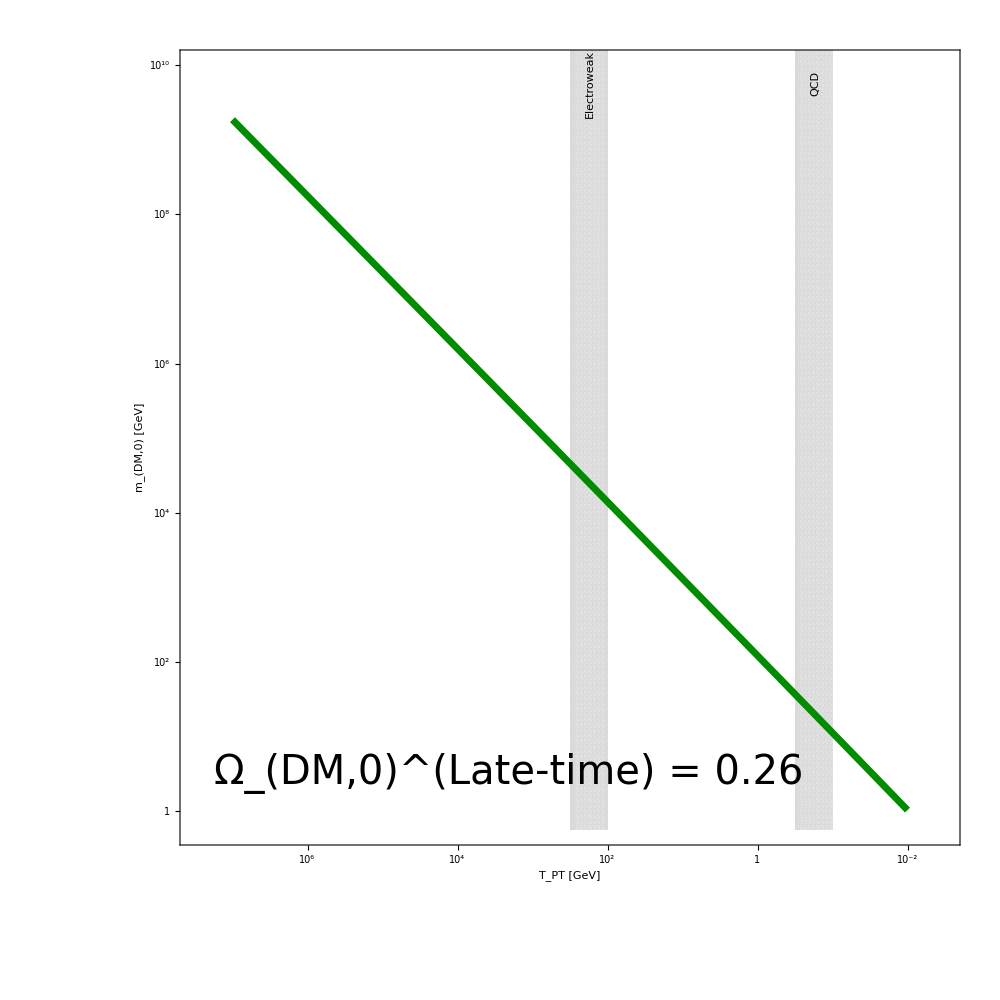

```mathematica
xMinRangeMasses=1.5;
xMaxRangeMasses=11.5;
yMinRangeMasses=-0.25;
yMaxRangeMasses=10;

PRangeMasses={{xMinRangeMasses,xMaxRangeMasses},{yMinRangeMasses,yMaxRangeMasses}};

colDMMass=RGBColor[0,0.55,0];

SmallFontSize=30;
MedFontSize=40;
LargeFontSize=45;

PQCD=RegionPlot[9.5≤x≤10 && -0.25≤y≤14,{x,-1,10},{y,-0.25,14},PlotPoints->200,BoundaryStyle->None,PlotStyle->{LightGray,Opacity[0.75]},PlotRange->PRangeMasses,AspectRatio->1,FrameLabel->{{"m_(DM,0) [GeV]",Rotate["Ω_(DM,0)^CMB/Ω_(DM,0)^(Late-time)",-180 Degree]},{"T_PT [GeV]",None}},LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->MedFontSize,Black},ImageSize->1000,Frame->True,Axes->False,FrameTicks->{{{{11,""},{10,"10^10"},{9,""},{8,"10^8"},{7,""},{6,"10^6"},{5,""},{4,"10^4"},{3,""},{2,"10^2"},{1,""},{0,"1"}},TabCorr},{{{1,"10^8"},{2,""},{3,"10^6"},{4,""},{5,"10^4"},{6,""},{7,"10^2"},{8,""},{9,"1"},{10,""},{11,"10^-2"}},None}},FrameStyle->Directive[Black,Thickness[0.0015]],PlotRangeClipping->True,ImagePadding->All,Epilog->{Inset[Rotate[Text[Style["QCD",FontFamily->"Latin Modern Roman",SmallFontSize,Black]],ArcTan[Infinity]],{9.7,yMaxRangeMasses-0.25},align[Top]],Inset[Rotate[Text[Style["Electroweak",FontFamily->"Latin Modern Roman",SmallFontSize,Black]],ArcTan[Infinity]],{6.7,yMaxRangeMasses-0.25},align[Top]],Text[Style["Ω_(DM,0)^(Late-time) = 0.26",FontFamily->"Latin Modern Roman",MedFontSize,Black],{1.75,yMinRangeMasses+0.75},align[Left]](*,{colDMMass,Thickness[0.005],Dashing[0.02],Line[{{1.75,1.75},{2.75,1.75}}]},Text[Style["g_Y = 10^-15",FontFamily->"Latin Modern Roman",SmallFontSize,Black],{3.0,1.75},align[Left]],{colDMMass,Thickness[0.005],Line[{{1.75,2.5},{2.75,2.5}}]},Text[Style["g_Y = 1",FontFamily->"Latin Modern Roman",SmallFontSize,Black],{3.0,2.5},align[Left]]*)}];

PEW=RegionPlot[6.5≤x≤7 && -0.25≤y≤14,{x,-1,10},{y,-0.25,14},PlotPoints->200,BoundaryStyle->None,PlotStyle->{LightGray,Opacity[0.75]}];

PlotMassPsiNow=Plot[TabMassFun[9-x],{x,2,11},PlotRange->PRangeMasses,PlotStyle-> {colDMMass,Thickness[0.005]}];
(*PlotMassPsiNowGyLow=Plot[TabMassFunGyLow[9-x],{x,2,11},PlotRange->PRangeMasses,PlotStyle-> {colDMMass,Dashing[0.02],Thickness[0.005]}];*)



(*Show[PQCD,PEW,PlotMassPsiNow,PlotMassPsiNowGyLow]*)
Show[PQCD,PEW,PlotMassPsiNow]
Export["/Users/sayanmandal/Documents/Physics/Projects/Scalar-DM-Neutrino/FigMassesNowNoScalar.pdf",Show[PQCD,PEW,PlotMassPsiNow],"PDF"];
```

## Ratio of Masses -- Various g_Y

```mathematica
(*gy1=10^-2;
gy2=10^-5;
gy3=10^-8;
(*gy4=10^-15;*)

TabMassRat1=Table[{TT,MPsi[gy1,ReturnLamb[gy1,10^TT],10^TT]/MPsi[1,ReturnLamb[1,10^TT],10^TT]},{TT,-2,7}];
TabMassRat2=Table[{TT,MPsi[gy2,ReturnLamb[gy2,10^TT],10^TT]/MPsi[1,ReturnLamb[1,10^TT],10^TT]},{TT,-2,7}];
TabMassRat3=Table[{TT,MPsi[gy3,ReturnLamb[gy3,10^TT],10^TT]/MPsi[1,ReturnLamb[1,10^TT],10^TT]},{TT,-2,7}];*)
```

```mathematica
(*TabMassRat1Int=Interpolation[TabMassRat1];
TabMassRat1Fun=Function[TabMassRat1Int[#]];

TabMassRat2Int=Interpolation[TabMassRat2];
TabMassRat2Fun=Function[TabMassRat2Int[#]];

TabMassRat3Int=Interpolation[TabMassRat3];
TabMassRat3Fun=Function[TabMassRat3Int[#]];
*)
```

```mathematica
(*MassRatXMin=1.5;
MassRatXMax=11.5;
MassRangeYMin=0.775;
MassRangeYMax=1.05;

PRangeMassRat={{MassRatXMin,MassRatXMax},{MassRangeYMin,MassRangeYMax}};

(*Color Palette*)

colgy1=Darker[Cyan,0.15];
colgy2=RGBColor["#A997DF"];
colgy3=RGBColor["#6FDE6E"];


PlotMassRat1=Plot[TabMassRat1Fun[9-x],{x,2,11},PlotRange->PRangeMassRat,PlotStyle-> {colgy1,Thickness[0.005]},AspectRatio->1.0,FrameLabel->{{"m_(DM,0)/m_(DM,0)^(g_Y = 1)",None},{"T_PT [GeV]",None}},LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->MedFontSize,Black},ImageSize->1000,Frame->True,Axes->False,FrameTicks->{{Automatic,None},{{{1,"10^8"},{2,""},{3,"10^6"},{4,""},{5,"10^4"},{6,""},{7,"10^2"},{8,""},{9,"1"},{10,""},{11,"10^-2"}},None}},FrameStyle->Directive[Black,Thickness[0.0015]],PlotRangeClipping->True,ImagePadding->All,Epilog->{Text[Style["Ω_(DM,0)^(Late-time) = 0.26",FontFamily->"Latin Modern Roman",40,Black],{11.25,MassRangeYMin+0.015},align[Right]],{colgy3,Thickness[0.005],Line[{{1.75,MassRangeYMin+0.015},{2.75,MassRangeYMin+0.015}}]},Text[Style["g_Y = 10^-8",FontFamily->"Latin Modern Roman",MedFontSize,Black],{3.0,MassRangeYMin+0.015},align[Left]],{colgy2,Thickness[0.005],Line[{{1.75,MassRangeYMin+0.03},{2.75,MassRangeYMin+0.03}}]},Text[Style["g_Y = 10^-5",FontFamily->"Latin Modern Roman",MedFontSize,Black],{3.0,MassRangeYMin+0.03},align[Left]],{colgy1,Thickness[0.005],Line[{{1.75,MassRangeYMin+0.045},{2.75,MassRangeYMin+0.045}}]},Text[Style["g_Y = 10^-2",FontFamily->"Latin Modern Roman",MedFontSize,Black],{3.0,MassRangeYMin+0.045},align[Left]]}];

PlotMassRat2=Plot[TabMassRat2Fun[9-x],{x,2,11},PlotRange->PRangeMassRat,PlotStyle-> {colgy2,Thickness[0.005]}];

PlotMassRat3=Plot[TabMassRat3Fun[9-x],{x,2,11},PlotRange->PRangeMassRat,PlotStyle-> {colgy3,Thickness[0.005]}];


Show[PlotMassRat1,PlotMassRat2,PlotMassRat3]
Export["/Users/sayanmandal/Documents/Physics/Projects/Scalar-DM-Neutrino/FigMassesRatioGy.pdf",Show[PlotMassRat1,PlotMassRat2,PlotMassRat3],"PDF"];*)
```

## Ratio of Ω_φ(z) to Ω_DM(z) -- Various T_PT

```mathematica
TPTM2=10^-2; (*GeV*)
TPT3=10^3; (*GeV*)
TPT7=10^7; (*GeV*)

LambM2=ReturnLamb[1,TPTM2];
Lamb3=ReturnLamb[1,TPT3];
Lamb7=ReturnLamb[1,TPT7];

TabOmPhiM2=Table[{0-x,Log10[OmegaPhiByOmegaDM[1,LambM2,TPTM2,10^x-1]]},{x,0,11,0.5}];
TabOmPhi3=Table[{0-x,Log10[OmegaPhiByOmegaDM[1,Lamb3,TPT3,10^x-1]]},{x,0,16,0.5}];
TabOmPhi7=Table[{0-x,Log10[OmegaPhiByOmegaDM[1,Lamb7,TPT7,10^x-1]]},{x,0,20,0.5}];
```

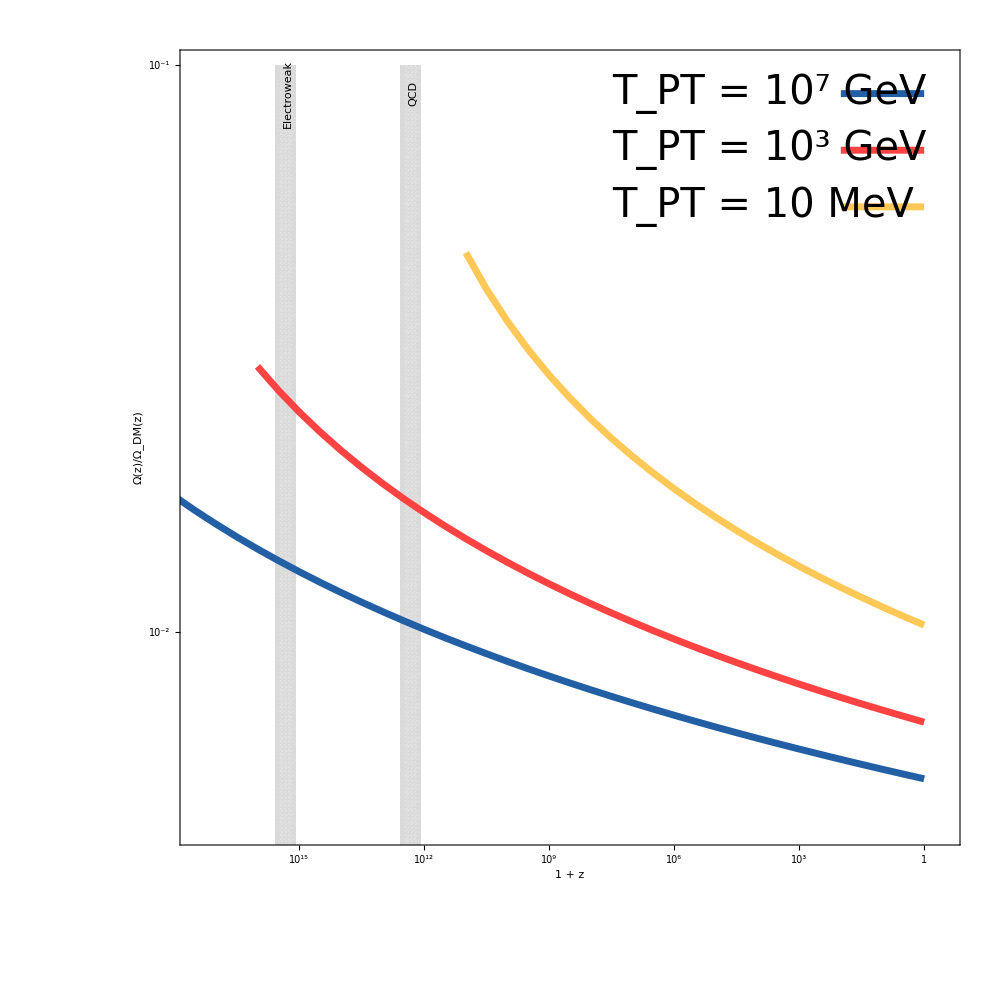

```mathematica
colM2=RGBColor["#FFC857"];
(*col2=RGBColor["#A691AE"];*)
col3=RGBColor["#FF4242"];
col7=RGBColor["#235FA4"];

xMinOmegaRange=-17.5;
xMaxOmegaRange=0.5;
yMinOmegaRange=-2.35;
yMaxOmegaRange=-1.0;

POmegaPhiRangeRev={{xMinOmegaRange,xMaxOmegaRange},{yMinOmegaRange,yMaxOmegaRange}};

(*SmallFontSize=35;*)

PEWOmPhiRatRev=RegionPlot[Log10[(1.25*10^15)^-1]≥x≥Log10[(3.76*10^15)^-1] && -2.5≤y≤-1.0,{x,-20,0},{y,-2.5,-1.0},PlotPoints->200,BoundaryStyle->None,PlotStyle->{LightGray,Opacity[0.75]},PlotRange->POmegaPhiRangeRev,AspectRatio->1.0,FrameLabel->{{"Ω(z)/Ω_DM(z)",None},{"1 + z",None}},LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->MedFontSize,Black},ImageSize->1000,Frame->True,FrameTicks->{{LogTicks[10,-2.5,-1.0,TickLengthScale->2],None},{{{0,"1"},{-1,""},{-2,""},{-3,"10^3"},{-4,""},{-5,""},{-6,"10^6"},{-7,""},{-8,""},{-9,"10^9"},{-10,""},{-11,""},{-12,"10^12"},{-13,""},{-14,""},{-15,"10^15"},{-16,""},{-17,""},{-18,"10^18"},{-19,""},{-20,""}},None}},FrameStyle->Directive[Black,Thickness[0.0015]],PlotRangeClipping->True,(*ImagePadding->{{130,15},{120,25}},*)ImagePadding->All,Epilog->{Text[Style["T_PT = 10^7 GeV",FontFamily->"Latin Modern Roman",MedFontSize,Black],{xMinOmegaRange+10,yMaxOmegaRange-0.05},align[Left]],{col7,Thickness[0.005],Line[{{-2,yMaxOmegaRange-0.05},{0,yMaxOmegaRange-0.05}}]},Text[Style["T_PT = 10^3 GeV",FontFamily->"Latin Modern Roman",MedFontSize,Black],{xMinOmegaRange+10,yMaxOmegaRange-0.15},align[Left]],{col3,Thickness[0.005],Line[{{-2,yMaxOmegaRange-0.15},{0,yMaxOmegaRange-0.15}}]},Text[Style["T_PT = 10 MeV",FontFamily->"Latin Modern Roman",MedFontSize,Black],{xMinOmegaRange+10,yMaxOmegaRange-0.25},align[Left]],{colM2,Thickness[0.005],Line[{{-2,yMaxOmegaRange-0.25},{0,yMaxOmegaRange-0.25}}]},Inset[Rotate[Text[Style["QCD",FontFamily->"Latin Modern Roman",SmallFontSize,Black]],ArcTan[Infinity]],{-(Log10[1.25*10^12]+Log10[3.76*10^12])/2-0.05,yMaxOmegaRange-0.05},align[Top]],Inset[Rotate[Text[Style["Electroweak",FontFamily->"Latin Modern Roman",SmallFontSize,Black]],ArcTan[Infinity]],{-(Log10[1.25*10^15]+Log10[3.76*10^15])/2-0.05,yMaxOmegaRange-0.05},align[Top]]}];

PQCDOmPhiRatRev=RegionPlot[Log10[(1.25)^-1*10^-12]≥x≥Log10[(3.76)^-1*10^-12] && -2.5≤y≤-1.0,{x,-20,0},{y,-2.5,-1.0},PlotPoints->200,BoundaryStyle->None,PlotStyle->{LightGray,Opacity[0.75]}];

PlotOmPhiRatM2Rev=ListPlot[TabOmPhiM2,PlotRange->POmegaPhiRangeRev,Joined->True,PlotStyle-> {colM2,Thickness[0.005]}];
PlotOmPhiRat3Rev=ListPlot[TabOmPhi3,PlotRange->POmegaPhiRangeRev,Joined->True,PlotStyle-> {col3,Thickness[0.005]}];
PlotOmPhiRat7Rev=ListPlot[TabOmPhi7,PlotRange->POmegaPhiRangeRev,Joined->True,PlotStyle-> {col7,Thickness[0.005]}];


Show[PEWOmPhiRatRev,PQCDOmPhiRatRev,PlotOmPhiRatM2Rev,PlotOmPhiRat3Rev,PlotOmPhiRat7Rev]
Export["/Users/sayanmandal/Documents/Physics/Projects/Scalar-DM-Neutrino/FigOmPhiZRev.pdf",Show[PEWOmPhiRatRev,PQCDOmPhiRatRev,PlotOmPhiRatM2Rev,PlotOmPhiRat3Rev,PlotOmPhiRat7Rev],"PDF"];
```

## Deviation of ρ_φ(z) from a^3 -- Various T_PT

```mathematica
TPTM2=10^-2; (*GeV*)
TPT3=10^3; (*GeV*)
TPT7=10^7; (*GeV*)

LambM2=ReturnLamb[1,TPTM2];
Lamb3=ReturnLamb[1,TPT3];
Lamb7=ReturnLamb[1,TPT7];

TabRhoPsiM2=Table[{0-x,Log10[RhoPsi[1,LambM2,TPTM2,10^x-1]]},{x,0,11,0.5}];
TabRhoPsi3=Table[{0-x,Log10[RhoPsi[1,Lamb3,TPT3,10^x-1]]},{x,0,16,0.5}];
TabRhoPsi7=Table[{0-x,Log10[RhoPsi[1,Lamb7,TPT7,10^x-1]]},{x,0,20,0.5}];

TabCompare=Table[{0-x,Log10[RhoPsi[1,Lamb7,TPT7,0]*(1+(10^x-1))^3]},{x,0,20,0.5}];
```

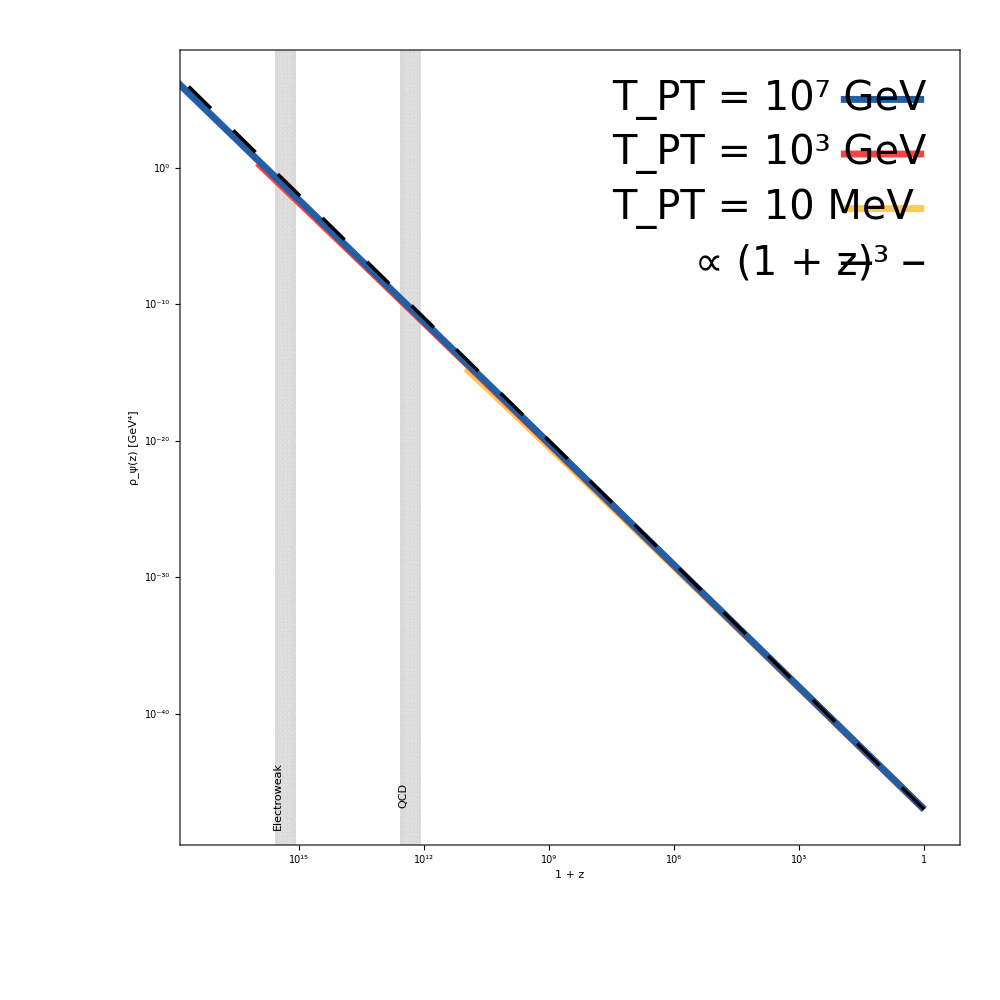

```mathematica
colM2=RGBColor["#FFC857"];
col3=RGBColor["#FF4242"];
col7=RGBColor["#235FA4"];

xMinOmegaPsi=-17.5;
xMaxOmegaPsi=0.5;
yMinOmegaPsi=-48.5;
yMaxOmegaPsi=7.5;

POmegaPsiRange={{xMinOmegaPsi,xMaxOmegaPsi},{yMinOmegaPsi,yMaxOmegaPsi}};

(*SmallFontSize=40;*)

PEWOmPsi=RegionPlot[Log10[(1.25*10^15)^-1]≥x≥Log10[(3.76*10^15)^-1] && -50≤y≤15,{x,-20,0},{y,-50,15},PlotPoints->200,BoundaryStyle->None,PlotStyle->{LightGray,Opacity[0.75]},PlotRange->POmegaPsiRange,AspectRatio->1.0,FrameLabel->{{"ρ_ψ(z) [GeV^4]",None},{"1 + z",None}},LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->MedFontSize,Black},ImageSize->1000,Frame->True,FrameTicks->{{LogTicks[10,-50,15,TickLengthScale->1,TickLabelStep->10,ShowMinorTicks->False],None},{{{0,"1"},{-1,""},{-2,""},{-3,"10^3"},{-4,""},{-5,""},{-6,"10^6"},{-7,""},{-8,""},{-9,"10^9"},{-10,""},{-11,""},{-12,"10^12"},{-13,""},{-14,""},{-15,"10^15"},{-16,""},{-17,""},{-18,"10^18"},{-19,""},{-20,""}},None}},FrameStyle->Directive[Black,Thickness[0.0015]],PlotRangeClipping->True,(*ImagePadding->{{150,10},{120,20}},*)ImagePadding->All,Epilog->{Text[Style["T_PT = 10^7 GeV",FontFamily->"Latin Modern Roman",MedFontSize,Black],{xMinOmegaPsi+10,yMaxOmegaPsi-2.5},align[Left]],{col7,Thickness[0.005],Line[{{-2,yMaxOmegaPsi-2.5},{0,yMaxOmegaPsi-2.5}}]},Text[Style["T_PT = 10^3 GeV",FontFamily->"Latin Modern Roman",MedFontSize,Black],{xMinOmegaPsi+10,yMaxOmegaPsi-6.5},align[Left]],{col3,Thickness[0.005],Line[{{-2,yMaxOmegaPsi-6.5},{0,yMaxOmegaPsi-6.5}}]},Text[Style["T_PT = 10 MeV",FontFamily->"Latin Modern Roman",MedFontSize,Black],{xMinOmegaPsi+10,yMaxOmegaPsi-10.5},align[Left]],{colM2,Thickness[0.005],Line[{{-2,yMaxOmegaPsi-10.5},{0,yMaxOmegaPsi-10.5}}]},Text[Style["∝ (1 + z)^3",FontFamily->"Latin Modern Roman",MedFontSize,Black],{xMinOmegaPsi+12,yMaxOmegaPsi-14.5},align[Left]],{Black,Thickness[0.0025],Dashing[0.0225],Line[{{-2,yMaxOmegaPsi-14.5},{0,yMaxOmegaPsi-14.5}}]},Inset[Rotate[Text[Style["QCD",FontFamily->"Latin Modern Roman",SmallFontSize,Black]],ArcTan[Infinity]],{-(Log10[1.25*10^12]+Log10[3.76*10^12])/2-0.05,yMinOmegaPsi+2.5},align[Bottom]],Inset[Rotate[Text[Style["Electroweak",FontFamily->"Latin Modern Roman",SmallFontSize,Black]],ArcTan[Infinity]],{-(Log10[1.25*10^15]+Log10[3.76*10^15])/2-0.05,yMinOmegaPsi+2.5},align[Bottom]]}];

PQCDOmPsi=RegionPlot[Log10[(1.25)^-1*10^-12]≥x≥Log10[(3.76)^-1*10^-12] && -50≤y≤15,{x,-20,0},{y,-50,15},PlotPoints->200,BoundaryStyle->None,PlotStyle->{LightGray,Opacity[0.75]}];

PlotOmPsiM2X=ListPlot[TabRhoPsiM2,PlotRange->POmegaPsiRange,Joined->True,PlotStyle-> {colM2,Thickness[0.005]}];
PlotOmPsi3X=ListPlot[TabRhoPsi3,PlotRange->POmegaPsiRange,Joined->True,PlotStyle-> {col3,Thickness[0.005]}];
PlotOmPsi7X=ListPlot[TabRhoPsi7,PlotRange->POmegaPsiRange,Joined->True,PlotStyle-> {col7,Thickness[0.005]}];

PlotCompare=ListPlot[TabCompare,PlotRange->POmegaPsiRange,Joined->True,PlotStyle-> {Black,Thickness[0.0025],Dashing[0.0225]}];

Show[PEWOmPsi,PQCDOmPsi,PlotOmPsiM2X,PlotOmPsi3X,PlotOmPsi7X,PlotCompare]
Export["/Users/sayanmandal/Documents/Physics/Projects/Scalar-DM-Neutrino/FigPsiEnDen.pdf",Show[PEWOmPsi,PQCDOmPsi,PlotOmPsiM2X,PlotOmPsi3X,PlotOmPsi7X,PlotCompare],"PDF"];
```

## Numerical Solution Using NDSolve -- Various T_PT

```mathematica
TPTM2=10^-2; (*GeV*)
TPT3=10^3; (*GeV*)
TPT7=10^7; (*GeV*)

gYY=10^0;

LambM2=ReturnLamb[gYY,TPTM2];
Lamb3=ReturnLamb[gYY,TPT3];
Lamb7=ReturnLamb[gYY,TPT7];


(*Relevant constants*)
aPTM2=1/(1+zPT[TPTM2]);
aPT3=1/(1+zPT[TPT3]);
aPT7=1/(1+zPT[TPT7]);


YM2=(3*LambM2^2*(MSc[gYY,LambM2,TPTM2])^2*MPl^2*aPTM2^4)/(OmegaRNow*ρCrNow);
AM2=Exp[-3/(R1[gYY,LambM2]-1)];

Y3=(3*Lamb3^2*(MSc[gYY,Lamb3,TPT3])^2*MPl^2*aPT3^4)/(OmegaRNow*ρCrNow);
A3=Exp[-3/(R1[gYY,Lamb3]-1)];

Y7=(3*Lamb7^2*(MSc[gYY,Lamb7,TPT7])^2*MPl^2*aPT7^4)/(OmegaRNow*ρCrNow);
A7=Exp[-3/(R1[gYY,Lamb7]-1)];


(*Initial Conditions*)
yyM20=3/(R1[gYY,LambM2]-1);
zzM20=3;
xxFinalM2=-Log[aPTM2];

yy30=3/(R1[gYY,Lamb3]-1);
zz30=3;
xxFinal3=-Log[aPT3];

yy70=3/(R1[gYY,Lamb7]-1);
zz70=3;
xxFinal7=-Log[aPT7];


(*Numerical Solutions*)

sM2=NDSolve[{yM2''[x]+yM2'[x]-YM2*Exp[4*x]*(Exp[-yM2[x]]-AM2*Exp[-3*x])==0,yM2[0]==yyM20,yM2'[0]==zzM20},yM2,{x,0,xxFinalM2},MaxSteps->10000000,WorkingPrecision->7];
TabSolNDM2=Table[{Log10[aPTM2*Exp[xx]],Evaluate[yM2[xx]/.sM2][[1]]},{xx,0,xxFinalM2,0.5}];

s3=NDSolve[{y3''[x]+y3'[x]-Y3*Exp[4*x]*(Exp[-y3[x]]-A3*Exp[-3*x])==0,y3[0]==yy30,y3'[0]==zz30},y3,{x,0,xxFinal3},MaxSteps->2000000,WorkingPrecision->10];
TabSolND3=Table[{Log10[aPT3*Exp[xx]],Evaluate[y3[xx]/.s3][[1]]},{xx,0,xxFinal3,0.5}];

s7=NDSolve[{y7''[x]+y7'[x]-Y7*Exp[4*x]*(Exp[-y7[x]]-A7*Exp[-3*x])==0,y7[0]==yy70,y7'[0]==zz70},y7,{x,0,xxFinal7},MaxSteps->20000000,WorkingPrecision->11];
TabSolND7=Table[{Log10[aPT7*Exp[xx]],Evaluate[y7[xx]/.s7][[1]]},{xx,0,xxFinal7,0.5}];


(*Analytic Solutions*)

YBarM2[x_]:=3*(1/(R1[gYY,LambM2]-1)+x)
TabYBarNormM2=Table[{Log10[aPTM2*Exp[x]],YBarM2[x]},{x,0,-Log[aPTM2],1}];

YBar3[x_]:=3*(1/(R1[gYY,Lamb3]-1)+x)
TabYBarNorm3=Table[{Log10[aPT3*Exp[x]],YBar3[x]},{x,0,-Log[aPT3],1}];

YBar7[x_]:=3*(1/(R1[gYY,Lamb7]-1)+x)
TabYBarNorm7=Table[{Log10[aPT7*Exp[x]],YBar7[x]},{x,0,-Log[aPT7],1}];
```

NDSolve::precw: The precision of the differential equation ({{-9.86241×10^39 ⅇ^(4 x) (-7.19981×10^-9 Power[«2»]+ⅇ^Times[«2»])+yM2'[x]+yM2''[x]==0,yM2[0]==18.7492,yM2'[0]==3},{},{},{},{}}) is less than WorkingPrecision (7.).

NDSolve::precw: The precision of the differential equation ({{-2.10064×10^30 ⅇ^(4 x) (-2.41995×10^-14 Power[«2»]+ⅇ^Times[«2»])+y3'[x]+y3''[x]==0,y3[0]==31.3524,y3'[0]==3},{},{},{},{}}) is less than WorkingPrecision (10.).

NDSolve::precw: The precision of the differential equation ({{-3.14422×10^22 ⅇ^(4 x) (-1.31223×10^-18 Power[«2»]+ⅇ^Times[«2»])+y7'[x]+y7''[x]==0,y7[0]==41.1748,y7'[0]==3},{},{},{},{}}) is less than WorkingPrecision (11.).

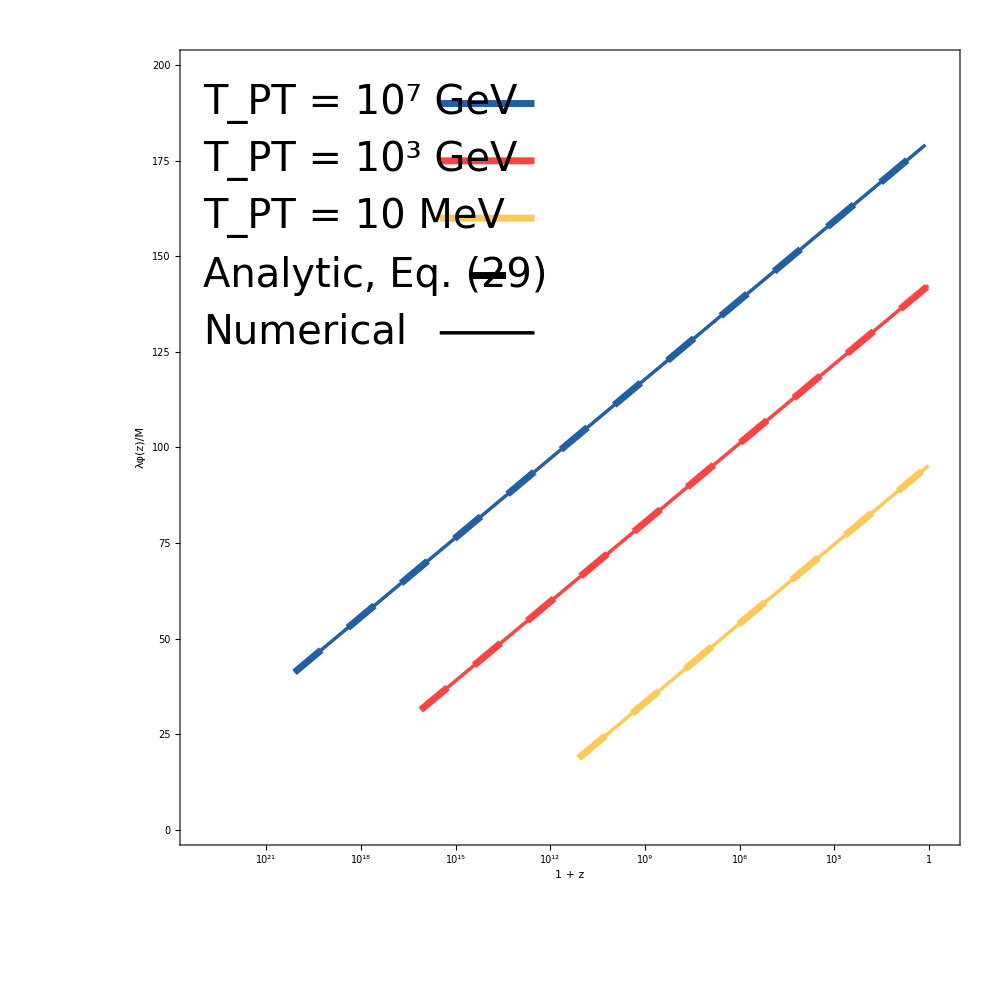

```mathematica
xMinCompare=-23.25;
xMaxCompare=0.5;
yMinCompare=0;
yMaxCompare=200;

PCompareSols={{xMinCompare,xMaxCompare},{yMinCompare,yMaxCompare}};

PlotPhiM2Norm=ListPlot[TabYBarNormM2,Joined->True,PlotStyle-> {Darker[colM2,0],Thickness[0.005],Dashing[0.025]},PlotRange->PCompareSols];
PlotPhi3Norm=ListPlot[TabYBarNorm3,Joined->True,PlotStyle-> {Darker[col3,0],Thickness[0.005],Dashing[0.025]},PlotRange->PCompareSols];
PlotPhi7Norm=ListPlot[TabYBarNorm7,Joined->True,PlotStyle-> {Darker[col7,0],Thickness[0.005],Dashing[0.025]},PlotRange->PCompareSols];

PlotPhiSolNDM2=ListPlot[TabSolNDM2,Joined->True,PlotStyle-> {colM2,Thickness[0.0025],Opacity[1]},PlotRange->PCompareSols,AspectRatio->1.0,FrameLabel->{{"λφ(z)/M",None},{"1 + z",None}},LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->MedFontSize,Black},ImageSize->1000,Frame->True,FrameTicks->{{Automatic,None},{{{0,"1"},{-1,""},{-2,""},{-3,"10^3"},{-4,""},{-5,""},{-6,"10^6"},{-7,""},{-8,""},{-9,"10^9"},{-10,""},{-11,""},{-12,"10^12"},{-13,""},{-14,""},{-15,"10^15"},{-16,""},{-17,""},{-18,"10^18"},{-19,""},{-20,""},{-21,"10^21"},{-22,""},{-23,""}},None}},FrameStyle->Directive[Black,Thickness[0.0015]],PlotRangeClipping->True,(*ImagePadding->{{115,15},{120,15}},*)ImagePadding->All,Epilog->{Text[Style["T_PT = 10^7 GeV",FontFamily->"Latin Modern Roman",MedFontSize,Black],{-23,190},align[Left]],{col7,Thickness[0.005],Line[{{-15.5,190},{-12.5,190}}]},Text[Style["T_PT = 10^3 GeV",FontFamily->"Latin Modern Roman",MedFontSize,Black],{xMinCompare+0.25,yMaxCompare-25},align[Left]],{col3,Thickness[0.005],Line[{{-15.5,yMaxCompare-25},{-12.5,yMaxCompare-25}}]},Text[Style["T_PT = 10 MeV",FontFamily->"Latin Modern Roman",MedFontSize,Black],{xMinCompare+0.25,yMaxCompare-40},align[Left]],{colM2,Thickness[0.005],Line[{{-15.5,yMaxCompare-40},{-12.5,yMaxCompare-40}}]},Text[Style["Analytic, Eq. (29)",FontFamily->"Latin Modern Roman",MedFontSize,Black],{xMinCompare+0.25,yMaxCompare-55},align[Left]],{Black,Thickness[0.005],Dashing[0.025],Line[{{-14.5,yMaxCompare-55},{-12.5,yMaxCompare-55}}]},Text[Style["Numerical",FontFamily->"Latin Modern Roman",MedFontSize,Black],{xMinCompare+0.25,yMaxCompare-70},align[Left]],{Black,Thickness[0.0025],Line[{{-15.5,yMaxCompare-70},{-12.5,yMaxCompare-70}}]}}];
PlotPhiSolND3=ListPlot[TabSolND3,Joined->True,PlotStyle-> {col3,Thickness[0.0025],Opacity[1]}];
PlotPhiSolND7=ListPlot[TabSolND7,Joined->True,PlotStyle-> {col7,Thickness[0.0025],Opacity[1]}];

Show[PlotPhiSolNDM2,PlotPhiSolND3,PlotPhiSolND7,PlotPhiM2Norm,PlotPhi3Norm,PlotPhi7Norm]
Export["/Users/sayanmandal/Documents/Physics/Projects/Scalar-DM-Neutrino/FigNumSolsND.pdf",Show[PlotPhiSolNDM2,PlotPhiSolND3,PlotPhiSolND7,PlotPhiM2Norm,PlotPhi3Norm,PlotPhi7Norm],"PDF"];
```

## Masses of φ and ψ -- Various T_PT

```mathematica
TPTM2=10^-2; (*GeV*)
TPT3=10^3; (*GeV*)
TPT7=10^7; (*GeV*)

gYY=1;

LambM2=ReturnLamb[gYY,TPTM2];
Lamb3=ReturnLamb[gYY,TPT3];
Lamb7=ReturnLamb[gYY,TPT7];


(*Relevant constants*)
aPTM2=1/(1+zPT[TPTM2]);
aPT3=1/(1+zPT[TPT3]);
aPT7=1/(1+zPT[TPT7]);

xPTM2=Log[aPTM2];
xPT3=Log[aPT3];
xPT7=Log[aPT7];


PhiBarM2[x_]:=(3*MSc[gYY,LambM2,TPTM2])/LambM2*(1/(R1[gYY,LambM2]-1)+x)
PhiBar3[x_]:=(3*MSc[gYY,Lamb3,TPT3])/Lamb3*(1/(R1[gYY,Lamb3]-1)+x)
PhiBar7[x_]:=(3*MSc[gYY,Lamb7,TPT7])/Lamb7*(1/(R1[gYY,Lamb7]-1)+x)

TabFermMassAfterM2=Table[{Log10[aPTM2*Exp[y]],Log10[gYY*PhiBarM2[y]]},{y,0,Abs[xPTM2],0.1}];
TabFermMassAfter3=Table[{Log10[aPT3*Exp[y]],Log10[gYY*PhiBar3[y]]},{y,0,Abs[xPT3],0.1}];
TabFermMassAfter7=Table[{Log10[aPT7*Exp[y]],Log10[gYY*PhiBar7[y]]},{y,0,Abs[xPT7],0.1}];
```

$Aborted

```mathematica
xMinMasses=-23.25;
xMaxMasses=0.5;
yMinMasses=-2;
yMaxMasses=14;

PMassesRange={{xMinMasses,xMaxMasses},{yMinMasses,yMaxMasses}};

PMassFermBeforeM2=Plot[Log10[30/x^2]-0.075,{x,-23.25,Log10[aPTM2]},PlotStyle-> {colM2,Thickness[0.005]},PlotRange->PMassesRange];
PMassFermBefore3=Plot[Log10[50/x^2]+5.25,{x,-23.25,Log10[aPT3]},PlotStyle-> {col3,Thickness[0.005]},PlotRange->PMassesRange];
PMassFermBefore7=Plot[Log10[70/x^2]+9.4,{x,-23.25,Log10[aPT7]},PlotStyle-> {col7,Thickness[0.005]},PlotRange->PMassesRange];


PMassScalarBeforeM2=Plot[Log10[(5*(1/22^2-1/(Log10[aPTM2])^2)^-1)/x^2-5/(Log10[aPTM2])^2*(1/22^2-1/(Log10[aPTM2])^2)^-1],{x,-23.25,Log10[aPTM2]},PlotStyle-> {colM2,Dashing[0.02],Thickness[0.005]},PlotRange->PMassesRange];
PMassScalarBefore3=Plot[Log10[(10^5*(1/22^2-1/(Log10[aPT3])^2)^-1)/x^2-10^5/(Log10[aPT3])^2*(1/22^2-1/(Log10[aPT3])^2)^-1],{x,-23.25,Log10[aPT3]},PlotStyle-> {col3,Dashing[0.02],Thickness[0.005]},PlotRange->PMassesRange];
PMassScalarBefore7=Plot[Log10[(10^10*(1/22^2-1/(Log10[aPT7])^2)^-1)/x^2-10^10/(Log10[aPT7])^2*(1/22^2-1/(Log10[aPT7])^2)^-1],{x,-23.25,Log10[aPT7]},PlotStyle-> {col7,Dashing[0.02],Thickness[0.005]},PlotRange->PMassesRange];
```

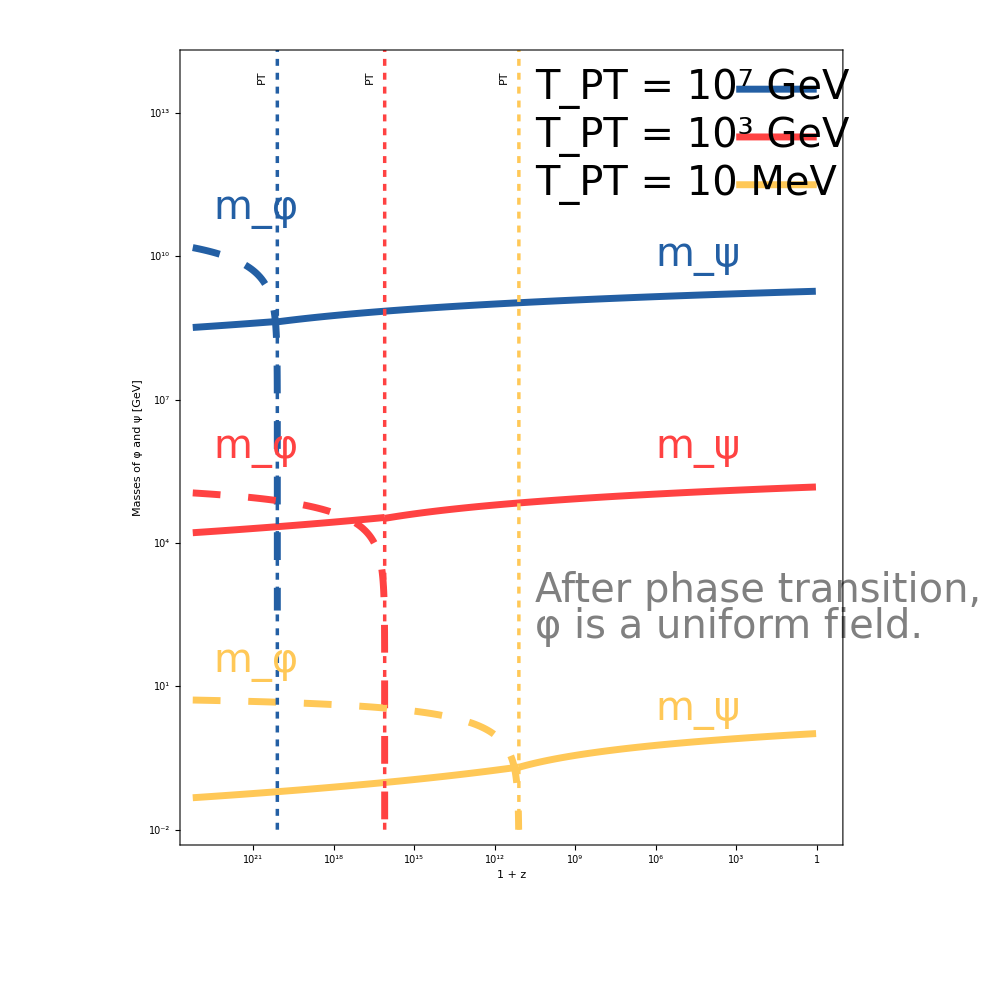

```mathematica
PMassFermAfterM2=ListPlot[TabFermMassAfterM2,Joined->True,PlotStyle-> {colM2,Thickness[0.005]},PlotRange->PMassesRange,AspectRatio->1.0,FrameLabel->{{"Masses of φ and ψ [GeV]",None},{"1 + z",None}},LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->MedFontSize,Black},ImageSize->1000,Frame->True,AxesOrigin->{0,-3},FrameTicks->{{LogTicks[10,-2,15,TickLengthScale->1,TickLabelStep->3,ShowMinorTicks->False],None},{{{0,"1"},{-1,""},{-2,""},{-3,"10^3"},{-4,""},{-5,""},{-6,"10^6"},{-7,""},{-8,""},{-9,"10^9"},{-10,""},{-11,""},{-12,"10^12"},{-13,""},{-14,""},{-15,"10^15"},{-16,""},{-17,""},{-18,"10^18"},{-19,""},{-20,""},{-21,"10^21"},{-22,""},{-23,""}},None}},FrameStyle->Directive[Black,Thickness[0.0015]],PlotRangeClipping->True,ImagePadding->All,(*ImagePadding->{{125,10},{115,10}},*)Epilog->{Text[Style["T_PT = 10^7 GeV",FontFamily->"Latin Modern Roman",MedFontSize,Black],{-10.5,yMaxMasses-0.5},align[Left]],{col7,Thickness[0.005],Line[{{-3,yMaxMasses-0.5},{0,yMaxMasses-0.5}}]},Text[Style["T_PT = 10^3 GeV",FontFamily->"Latin Modern Roman",MedFontSize,Black],{-10.5,yMaxMasses-1.5},align[Left]],{col3,Thickness[0.005],Line[{{-3,yMaxMasses-1.5},{0,yMaxMasses-1.5}}]},Text[Style["T_PT = 10 MeV",FontFamily->"Latin Modern Roman",MedFontSize,Black],{-10.5,yMaxMasses-2.5},align[Left]],{colM2,Thickness[0.005],Line[{{-3,yMaxMasses-2.5},{0,yMaxMasses-2.5}}]},{colM2,Thickness[0.0025],Dashing[0.005],Line[{{Log10[aPTM2],-2},{Log10[aPTM2],15}}]},Inset[Rotate[Text[Style["PT",FontFamily->"Latin Modern Roman",MedFontSize,colM2]],ArcTan[Infinity]],{Log10[aPTM2]-0.75,yMaxMasses-0.25},align[Top]],{col3,Thickness[0.0025],Dashing[0.005],Line[{{Log10[aPT3],-2},{Log10[aPT3],15}}]},Inset[Rotate[Text[Style["PT",FontFamily->"Latin Modern Roman",MedFontSize,col3]],ArcTan[Infinity]],{Log10[aPT3]-0.75,yMaxMasses-0.25},align[Top]],{col7,Thickness[0.0025],Dashing[0.005],Line[{{Log10[aPT7],-2},{Log10[aPT7],15}}]},Inset[Rotate[Text[Style["PT",FontFamily->"Latin Modern Roman",MedFontSize,col7]],ArcTan[Infinity]],{Log10[aPT7]-0.75,yMaxMasses-0.25},align[Top]],Text[Style["m_ψ",FontFamily->"Latin Modern Roman",MedFontSize,col7],{-6,10},align[Left]],Text[Style["m_ψ",FontFamily->"Latin Modern Roman",MedFontSize,col3],{-6,6},align[Left]],Text[Style["m_ψ",FontFamily->"Latin Modern Roman",MedFontSize,colM2],{-6,0.5},align[Left]],Text[Style["m_φ",FontFamily->"Latin Modern Roman",MedFontSize,col7],{-22.5,11},align[Left]],Text[Style["m_φ",FontFamily->"Latin Modern Roman",MedFontSize,col3],{-22.5,6},align[Left]],Text[Style["m_φ",FontFamily->"Latin Modern Roman",MedFontSize,colM2],{-22.5,1.5},align[Left]],Text[Style["After phase transition,",FontFamily->"Latin Modern Roman",MedFontSize,Gray],{-10.5,yMinMasses+5},align[Left]],Text[Style["φ is a uniform field.",FontFamily->"Latin Modern Roman",MedFontSize,Gray],{-10.5,yMinMasses+4.25},align[Left]]}];
PMassFermAfter3=ListPlot[TabFermMassAfter3,Joined->True,PlotStyle-> {col3,Thickness[0.005]},PlotRange->PMassesRange,AspectRatio->0.75];
PMassFermAfter7=ListPlot[TabFermMassAfter7,Joined->True,PlotStyle-> {col7,Thickness[0.005]},PlotRange->PMassesRange,AspectRatio->0.75];



Show[PMassFermAfterM2,PMassFermAfter3,PMassFermAfter7,PMassFermBeforeM2,PMassFermBefore3,PMassFermBefore7,PMassScalarBefore7,PMassScalarBefore3,PMassScalarBeforeM2]
Export["/Users/sayanmandal/Documents/Physics/Projects/Scalar-DM-Neutrino/FigMassesWithZ.pdf",Show[PMassFermAfterM2,PMassFermAfter3,PMassFermAfter7,PMassFermBeforeM2,PMassFermBefore3,PMassFermBefore7,PMassScalarBefore7,PMassScalarBefore3,PMassScalarBeforeM2],"PDF"];
```

## Equation of State -- Various T_PT

```mathematica
TPTM2=10^-2; (*GeV*)
TPT3=10^3; (*GeV*)
TPT7=10^7; (*GeV*)

LambM2=ReturnLamb[1,TPTM2];
Lamb3=ReturnLamb[1,TPT3];
Lamb7=ReturnLamb[1,TPT7];

aPTM2=1/(1+zPT[TPTM2]);
aPT3=1/(1+zPT[TPT3]);
aPT7=1/(1+zPT[TPT7]);

wPTM2=wPT[1,LambM2];
wPT3=wPT[1,Lamb3];
wPT7=wPT[1,Lamb7];


TabWM2={{-23.5,1/3},{-15,0.15},{Log10[aPTM2],wPTM2}};
TabW3={{-23.5,1/3},{-21,0.3},{Log10[aPT3],wPT3}};
TabW7={{-23.5,1/3},{-22,0.25},{Log10[aPT7],wPT7}};

WM2=Normal[NonlinearModelFit[TabWM2,b1*x^2+c1*x+d1,{b1,c1,d1},{x}]]
W3=Normal[NonlinearModelFit[TabW3,b3*x^2+c3*x+d3,{b3,c3,d3},{x}]]
W7=Normal[NonlinearModelFit[TabW7,b4*x^2+c4*x+d4,{b4,c4,d4},{x}]]
```

-0.994923-0.111281 x-0.00233019 x^2

-3.57284-0.337308 x-0.00728032 x^2

-14.3356-1.23164 x-0.025848 x^2

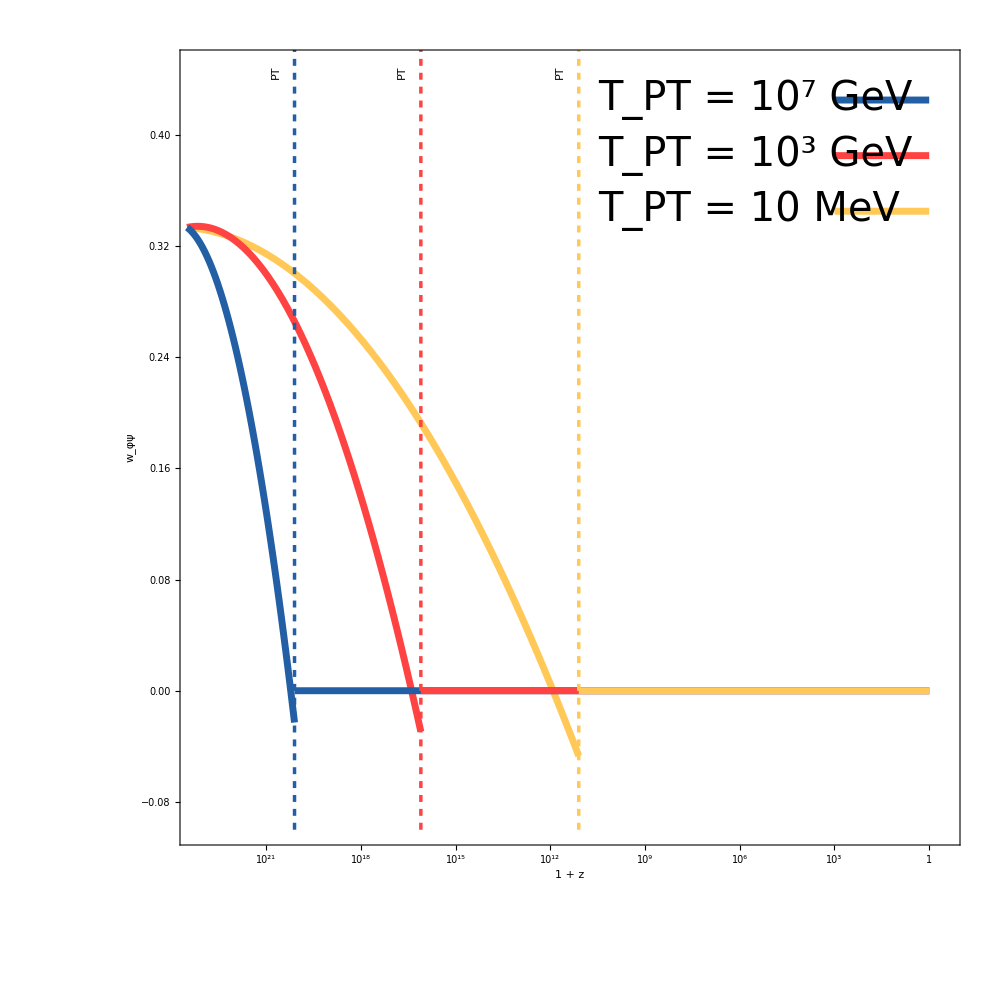

```mathematica
xMinEos=-23.25;
xMaxEos=0.5;
yMinEos=-0.1;
yMaxEos=0.45;

PEoSRange={{xMinEos,xMaxEos},{yMinEos,yMaxEos}};

PEoSM2=Plot[WM2,{x,-23.5,Log10[aPTM2]},PlotStyle-> {colM2,Thickness[0.005]},PlotRange->PEoSRange,AspectRatio->1.0,FrameLabel->{{"w_φψ",None},{"1 + z",None}},LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->MedFontSize,Black},ImageSize->1000,Frame->True,AxesOrigin->{0,-1},FrameTicks->{{Automatic,None},{{{0,"1"},{-1,""},{-2,""},{-3,"10^3"},{-4,""},{-5,""},{-6,"10^6"},{-7,""},{-8,""},{-9,"10^9"},{-10,""},{-11,""},{-12,"10^12"},{-13,""},{-14,""},{-15,"10^15"},{-16,""},{-17,""},{-18,"10^18"},{-19,""},{-20,""},{-21,"10^21"},{-22,""},{-23,""}},None}},FrameStyle->Directive[Black,Thickness[0.0015]],PlotRangeClipping->True,ImagePadding->All,Epilog->{Text[Style["T_PT = 10^7 GeV",FontFamily->"Latin Modern Roman",MedFontSize,Black],{-10.5,yMaxEos-0.025},align[Left]],{col7,Thickness[0.005],Line[{{-3,yMaxEos-0.025},{0,yMaxEos-0.025}}]},Text[Style["T_PT = 10^3 GeV",FontFamily->"Latin Modern Roman",MedFontSize,Black],{-10.5,yMaxEos-0.065},align[Left]],{col3,Thickness[0.005],Line[{{-3,yMaxEos-0.065},{0,yMaxEos-0.065}}]},Text[Style["T_PT = 10 MeV",FontFamily->"Latin Modern Roman",MedFontSize,Black],{-10.5,yMaxEos-0.105},align[Left]],{colM2,Thickness[0.005],Line[{{-3,yMaxEos-0.105},{0,yMaxEos-0.105}}]},{colM2,Thickness[0.0025],Dashing[0.005],Line[{{Log10[aPTM2],-0.1},{Log10[aPTM2],0.5}}]},Inset[Rotate[Text[Style["PT",FontFamily->"Latin Modern Roman",MedFontSize,colM2]],ArcTan[Infinity]],{Log10[aPTM2]-0.75,yMaxEos-0.005},align[Top]],{col3,Thickness[0.0025],Dashing[0.005],Line[{{Log10[aPT3],-0.1},{Log10[aPT3],0.5}}]},Inset[Rotate[Text[Style["PT",FontFamily->"Latin Modern Roman",MedFontSize,col3]],ArcTan[Infinity]],{Log10[aPT3]-0.75,yMaxEos-0.005},align[Top]],{col7,Thickness[0.0025],Dashing[0.005],Line[{{Log10[aPT7],-0.1},{Log10[aPT7],0.5}}]},Inset[Rotate[Text[Style["PT",FontFamily->"Latin Modern Roman",MedFontSize,col7]],ArcTan[Infinity]],{Log10[aPT7]-0.75,yMaxEos-0.005},align[Top]]}];

PEoS3=Plot[W3,{x,-23.5,Log10[aPT3]},PlotStyle-> {col3,Thickness[0.005]},PlotRange->PEoSRange];

PEoS7=Plot[W7,{x,-23.5,Log10[aPT7]},PlotStyle-> {col7,Thickness[0.005]},PlotRange->PEoSRange];

PEoSAfterM2=Plot[0,{x,Log10[aPTM2],0},PlotStyle-> {colM2,Thickness[0.005]},PlotRange->PEoSRange];
PEoSAfter3=Plot[0,{x,Log10[aPT3],0},PlotStyle-> {col3,Thickness[0.005]},PlotRange->PEoSRange];
PEoSAfter7=Plot[0,{x,Log10[aPT7],0},PlotStyle-> {col7,Thickness[0.005]},PlotRange->PEoSRange];

Show[PEoSM2,PEoS3,PEoS7,PEoSAfter7,PEoSAfter3,PEoSAfterM2]
Export["/Users/sayanmandal/Documents/Physics/Projects/Scalar-DM-Neutrino/FigEoS.pdf",Show[PEoSM2,PEoS3,PEoS7,PEoSAfter7,PEoSAfter3,PEoSAfterM2],"PDF"];
```

## Normalized Free Energy -- Various T_PT

```mathematica
TPTM2=10^-2; (*GeV*)
TPT7=10^7; (*GeV*)

LambM2=ReturnLamb[1,TPTM2];
Lamb7=ReturnLamb[1,TPT7];

DelPTM2=DelPT[1,ReturnLamb[1,TPTM2]];
DelPT7=DelPT[1,ReturnLamb[1,TPT7]];


kappaPTM2=(1*PhiPT[1,ReturnLamb[1,TPTM2],TPTM2])/TPTM2;
kappaPT7=(1*PhiPT[1,ReturnLamb[1,TPT7],TPT7])/TPT7;

FRFJM2[del_,k_]:=Exp[-(k*LambM2)/(del*1)]-2/(3 Pi^2 del^4)*NIntegrate[((x^2-k^2)^(3/2))/(Exp[x]+1),{x,k,Infinity}]
FRFJ7[del_,k_]:=Exp[-(k*Lamb7)/(del*1)]-2/(3 Pi^2 del^4)*NIntegrate[((x^2-k^2)^(3/2))/(Exp[x]+1),{x,k,Infinity}]
```

```mathematica
MinBeforePTM2=FindMinimum[FRFJM2[DelPTM2/1.75,xx],{xx,1}];//Quiet
MinBeforePT7=FindMinimum[FRFJ7[DelPT7/1.75,xx],{xx,1}];//Quiet

KappaMinM2=xx/.MinBeforePTM2[[2]];
KappaMin7=xx/.MinBeforePT7[[2]];
```

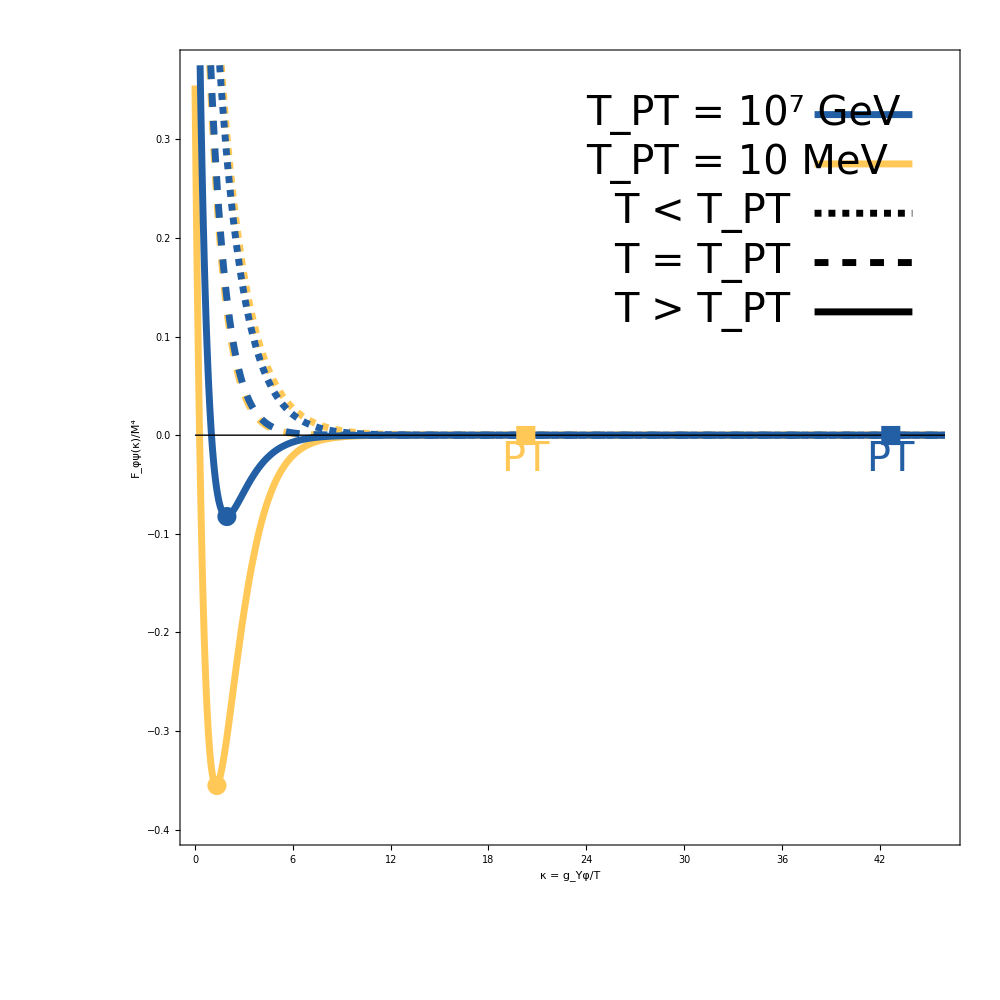

```mathematica
xMin=0;
xMax=46.0;
yMin=-0.4;
yMax=0.375;
FRRange={{xMin,xMax},{yMin,yMax}};

MinPos=-0.16;

PlotFRM2PT=Plot[FRFJM2[DelPTM2,x],{x,xMin,xMax},PlotStyle->{colM2,Thickness[0.005],Dashing[0.01]},Frame->True,PlotRange->FRRange,AspectRatio->1,ImageSize->1000,PlotLegends->Automatic,FrameLabel->{{"F_φψ(κ)/M^4",None},{"κ = g_Yφ/T",None}},LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->MedFontSize,Black},FrameStyle->Directive[Black,Thickness[0.0015]],PlotRangeClipping->True,ImagePadding->All,AxesOrigin->{-10,-10},Epilog->{Text[Style["■",FontFamily->"Latin Modern Roman",25,colM2],{kappaPTM2,FRFJM2[DelPTM2,kappaPTM2]}],Text[Style["PT",FontFamily->"Latin Modern Roman",MedFontSize,colM2],{kappaPTM2,FRFJM2[DelPTM2,kappaPTM2]-0.025}],Text[Style["●",FontFamily->"Latin Modern Roman",25,colM2],{KappaMinM2,MinBeforePTM2[[1]]}],Text[Style["■",FontFamily->"Latin Modern Roman",25,col7],{kappaPT7,FRFJ7[DelPT7,kappaPT7]}],Text[Style["PT",FontFamily->"Latin Modern Roman",MedFontSize,col7],{kappaPT7,FRFJ7[DelPT7,kappaPT7]-0.025}],Text[Style["●",FontFamily->"Latin Modern Roman",25,col7],{KappaMin7,MinBeforePT7[[1]]}],{Black,Thickness[0.001],Line[{{xMin,0},{xMax,0}}]},Text[Style["T_PT = 10^7 GeV",FontFamily->"Latin Modern Roman",MedFontSize,Black],{24,yMax-0.05},align[Left]],{col7,Thickness[0.005],Line[{{38,yMax-0.05},{44,yMax-0.05}}]},Text[Style["T_PT = 10 MeV",FontFamily->"Latin Modern Roman",MedFontSize,Black],{24,yMax-0.1},align[Left]],{colM2,Thickness[0.005],Line[{{38,yMax-0.1},{44,yMax-0.1}}]},Text[Style["T < T_PT",FontFamily->"Latin Modern Roman",MedFontSize,Black],{36.5,yMax-0.15},align[Right]],{Black,Thickness[0.005],Dashing[0.005],Line[{{38,yMax-0.15},{44,yMax-0.15}}]},Text[Style["T = T_PT",FontFamily->"Latin Modern Roman",MedFontSize,Black],{36.5,yMax-0.2},align[Right]],{Black,Thickness[0.005],Dashing[0.01],Line[{{38,yMax-0.2},{44,yMax-0.2}}]},Text[Style["T > T_PT",FontFamily->"Latin Modern Roman",MedFontSize,Black],{36.5,yMax-0.25},align[Right]],{Black,Thickness[0.005],Line[{{38,yMax-0.25},{44,yMax-0.25}}]}}];
PlotFRM2BeforePT=Plot[FRFJM2[DelPTM2/1.75,x],{x,xMin,xMax},PlotStyle->{colM2,Thickness[0.005]},Frame->True,PlotRange->FRRange];
PlotFRM2AfterPT=Plot[FRFJM2[DelPTM2*1.55,x],{x,xMin,xMax},PlotStyle->{colM2,Thickness[0.005],Dashing[0.005]},Frame->True,PlotRange->FRRange];

PlotFR7PT=Plot[FRFJ7[DelPT7,x],{x,xMin,xMax},PlotStyle->{col7,Thickness[0.005],Dashing[0.01]},Frame->True,PlotRange->FRRange];
PlotFR7BeforePT=Plot[FRFJ7[DelPT7/1.75,x],{x,xMin,xMax},PlotStyle->{col7,Thickness[0.005]},Frame->True,PlotRange->FRRange];
PlotFR7AfterPT=Plot[FRFJ7[DelPT7*1.5,x],{x,xMin,xMax},PlotStyle->{col7,Thickness[0.005],Dashing[0.005]},Frame->True,PlotRange->FRRange];

Show[PlotFRM2PT,PlotFRM2BeforePT,PlotFRM2AfterPT,PlotFR7PT,PlotFR7BeforePT,PlotFR7AfterPT]
Export["/Users/sayanmandal/Documents/Physics/Projects/Scalar-DM-Neutrino/FigFRNorm.pdf",Show[PlotFRM2PT,PlotFRM2BeforePT,PlotFRM2AfterPT,PlotFR7PT,PlotFR7BeforePT,PlotFR7AfterPT],"PDF"];
```

```mathematica
FF7[del_,k_]:=-2/(3 Pi^2 del^4)*NIntegrate[((x^2-k^2)^(3/2))/(Exp[x]+1),{x,k,Infinity}]
USca[del_,k_]:=Exp[-(k*Lamb7)/(del*1)]

USca[DelPT7/1.75,KappaMin7]
FRFJ7[DelPT7/1.75,KappaMin7]
FRFJ7[DelPT7,kappaPT7]
```

0.036312

-0.0790725

-4.85137×10^-21

```mathematica
KappaMin7
```

1.96247

```mathematica
MinBeforePT7[[1]]
```

-0.0790725

```mathematica
TabOmegaRat
```

{{-2,0.782773},{-1,0.802392},{0,0.818719},{1,0.832524},{2,0.844355},{3,0.854609},{4,0.863583},{5,0.871506},{6,0.878552},{7,0.884859},{8,0.89054},{9,0.895683},{10,0.900361},{11,0.904635},{12,0.908556},{13,0.912165},{14,0.915499},{15,0.918587},{16,0.921457},{17,0.924131}}